## Simulations for Top Down Model

Notes:
	- n_i is the branching factor at level i
	- ϵ is the total privacy budget and ϵ_i is the privacy budget at level i

```mathematica
SetDirectory[NotebookDirectory[]];
```

### 2 Deep Hierarchy

Recreate Aloni’s 2 Deep Hierarchy with sliders for total epsilon and n_2.

```mathematica
Var[n2_, x_, eps_] := 2*(1/(n2^2 * x^2) + (n2 - 1)/(n2*(eps-x)^2))
```

```mathematica
Manipulate[Plot[Var[n2, x, eps], {x, 0, eps} , AxesLabel->{Subscript[ϵ, 1], "Var(E_(1  j))"}], {{n2, 10, Subscript[n, 2]}, 1,20,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}]
```

```mathematica
min= Function[{n, e}, Minimize[{Var[n, x, e], x ≥ 0 && x≤ e},x]]
```

Function[{n,e},Minimize[{Var[n,x,e],x≥0&&x≤e},x]]

```mathematica
Manipulate[Plot[Var[n2, x, eps], {x, 0, eps} ,Epilog->{Red,PointSize->Large,Point[{x /.Last[min[n2,eps]],First[min[n2,eps]]}]}, AxesLabel->{Subscript[ϵ, 1], "Var(E_(1  j))"}], {{n2, 10, Subscript[n, 2]}, 1,20,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}]
```

### 3 Deep Hierarchy

Questions:
	 - What is the shape of the variance plot as we vary ϵ_1, ϵ_2, and ϵ_3? 
	 - Error over 50% of bottom level units, with cancelation.

```mathematica
Var1j[n2_, e1_, e2_] = 2*(1/(n2^2 * e1^2) + (n2 - 1)/(n2*e2^2))
```

2 (1/(e1^2 n2^2)+(-1+n2)/(e2^2 n2))

```mathematica
Var1jk[n2_,n3_, e1_, e2_,e3_] = 2*(1/(e3^2) + 1/(e3^2 * n3)) + (Var1j[n2, e1, e2] / n3^2)
```

2 (1/e3^2+1/(e3^2 n3))+(2 (1/(e1^2 n2^2)+(-1+n2)/(e2^2 n2)))/n3^2

Interactive Plot for variance on random variable of 3rd level of the hierarchy.   n_3 and the ratio between ϵ_1 and ϵ_2 have the most effect on the variance of ϵ_3.  n_2has a subtle effect on shape and ϵ adjusts scale.

```mathematica
Manipulate[ With[{e2share = 1 - e1share}, Plot[Var1jk[n2,n3, (1-e3)*e1share*eps ,(1-e3)*e2share*eps , e3*eps], {e3, 0, 1} , AxesLabel->{Subscript[ϵ, 3], "Var(E_(1  jk))"}]], {{n2, 10, Subscript[n, 2]}, 1,20,1,Appearance->"Labeled"},{{n3, 10, Subscript[n, 3]}, 1,20,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}, {{e1share,0.5, Subscript[ϵ, 1]/(Subscript[ϵ, 1]+Subscript[ϵ, 2])}, 0.0001,0.9999,Appearance->"Labeled"}]
```

```mathematica
Manipulate[  Plot[Var1jk[n2,n3, (1-e3)*e1share*eps ,(1-e3)*( 1 - e1share)*eps , e3*eps], {e1share, 0, 1} , AxesLabel->{Subscript[ϵ, 1]/(Subscript[ϵ, 1]+Subscript[ϵ, 2]), "Var(E_(1  jk))"}], {{n2, 10, Subscript[n, 2]}, 1,20,1,Appearance->"Labeled"},{{n3, 10, Subscript[n, 3]}, 1,20,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}, {{e3,0.65, Subscript[ϵ, 3]}, 0.0001,0.9999,Appearance->"Labeled"}]
```

```mathematica
Manipulate[ Plot[Var1j[n2, (1-e2)*eps , e2*eps], {e2, 0, 1} , AxesLabel->{Subscript[ϵ, 2], "Var(E_(1  j))"}], {{n2, 10, Subscript[n, 2]}, 1,20,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}]
```

### Error in “District” composed of half the bottom-level

```mathematica
SampleE1j[e1_,e2_, n2_] := With[ {L1 = LaplaceDistribution[0, 1/e1], L2 =  LaplaceDistribution[0, 1/e2] }, RandomVariate[L1]/ n2 + RandomVariate[L2] -  Total[RandomVariate[ProductDistribution[{L2, n2}]]]]
```

```mathematica
SampleE1jk[e1_,e2_,e3_, n2_, n3_] := With[{L1 = LaplaceDistribution[0, 1/e1], L2 =  LaplaceDistribution[0, 1/e2], L3 = LaplaceDistribution[0, 1/e3]},RandomVariate[L3] + (-Total[RandomVariate[ProductDistribution[{L3, n3}]]] + SampleE1j[e1, e2, n2])/n3]
```

```mathematica
Manipulate[ 
sample = Array[Function[b, Total[Array[Function[a, SampleE1jk[e1*eps, e2*eps,(1- e1 - e2)*eps, n2,n3]], Round[(n2*n3)/k]]]],500];
Show[Histogram[sample, Automatic, "PDF", AxesLabel->{Subscript["E", 3,Subscript[dist, k]]}],SmoothHistogram[sample]],{{k, 2, k}, 2,10,1,Appearance->"Labeled"}, {{n2, 4, Subscript[n, 2]}, 1,10,1,Appearance->"Labeled"},{{n3, 4, Subscript[n, 3]}, 1,10,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}, {{e1,0.25, Subscript[ϵ, 1]}, 0.001,1-e2,Appearance->"Labeled"},{{e2,0.25, Subscript[ϵ, 2]}, 0.001,1 - e1,Appearance->"Labeled"}, ContinuousAction->False]
```

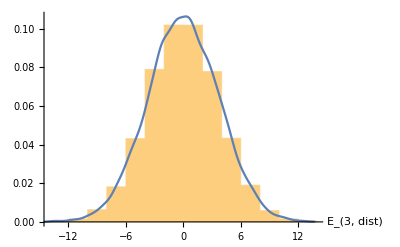

```mathematica
With[{n2=5, n3=4, eps=4, e1=0.25, e2=0.25}, 
data = Array[Function[b, Total[Array[Function[a, SampleE1jk[e1*eps, e2*eps,(1- e1 - e2)*eps, n2,n3]], Round[(n2*n3)/2]]]],10000];Show[Histogram[data, Automatic, "PDF", AxesLabel->{"E_(3, dist)"}],SmoothHistogram[data]]]
```

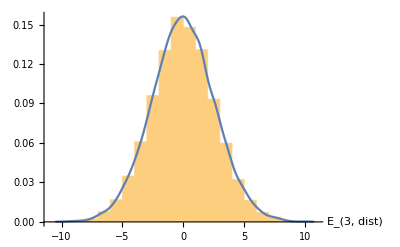

```mathematica
With[{n2=5, n3=4, eps=4, e1=0.25, e2=0.25}, 
data = Array[Function[b, Total[Array[Function[a, SampleE1jk[e1*eps, e2*eps,(1- e1 - e2)*eps, n2,n3]], Round[(n2*n3)/4]]]],10000];Show[Histogram[data, Automatic, "PDF", AxesLabel->{"E_(3, dist)"}],SmoothHistogram[data]]]
```

Error at one instance at third level

```mathematica
Manipulate[ Histogram[Array[Function[b,SampleE1jk[e1*eps, e2*eps,(1- e1 - e2)*eps, n2,n3]], 500],AxesLabel->{"E_(1  jk)"}], {{n2, 4, Subscript[n, 2]}, 1,10,1,Appearance->"Labeled"},{{n3, 4, Subscript[n, 3]}, 1,10,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 2,8,Appearance->"Labeled"}, {{e1,0.25, Subscript[ϵ, 1]}, 0.001,1-e2,Appearance->"Labeled"},{{e2,0.25, Subscript[ϵ, 2]}, 0.001,1 - e1,Appearance->"Labeled"}, ContinuousAction->False]
```

### Absolute Error

```mathematica
L1 = LaplaceDistribution[0, 1/e1]
```

LaplaceDistribution[0,1/e1]

```mathematica
L2 = LaplaceDistribution[0, 1/e2]
```

LaplaceDistribution[0,1/e2]

```mathematica
L3 = LaplaceDistribution[0, 1/e3]
```

LaplaceDistribution[0,1/e3]

```mathematica
AbsExpectationE1j[n2_]:= Expectation[Abs[x/n2 + y - Module[{k},Sum[Subscript[x, k],{k,1,n2}]]/n2], {x\[Distributed] L1, y \[Distributed] L2, Reduce`FreeVariables[Module[{k},Sum[Subscript[x, k],{k,1,n2}]]] \[Distributed]ProductDistribution[{L2, n2}]}]
```

```mathematica
AbsExpectationE1jk[n2_, n3_] := Expectation[Abs[u-Module[{k},Sum[Subscript[v, k],{k,1,n3}]]/n3 + (x/n2 + y - Module[{k},Sum[Subscript[x, k],{k,1,n2}]]/n2)/n3], {x\[Distributed] L1, y \[Distributed] L2, Reduce`FreeVariables[Module[{k},Sum[Subscript[x, k],{k,1,n2}]]] \[Distributed]ProductDistribution[{L2, n2}], u \[Distributed] L3, Reduce`FreeVariables[Module[{k},Sum[Subscript[v, k],{k,1,n3}]]] \[Distributed]ProductDistribution[{L3, n3}]}]
```

### Pull in cluster results for absolute error

#### 2nd Level

```mathematica
<< "AbsErrorTableE1j.wl"
```

{{1,(3 e1^3+6 e1^2 e2+4 e1 e2^2+2 e2^3)/(2 e1 e2 (e1+e2)^2)},{2,(94 e1^4+235 e1^3 e2+198 e1^2 e2^2+72 e1 e2^3+18 e2^4)/(36 e1 e2 (e1+e2)^2 (2 e1+e2))},{3,(2817 e1^5+9390 e1^4 e2+11421 e1^3 e2^2+6144 e1^2 e2^3+1536 e1 e2^4+256 e2^5)/(768 e1 e2 (e1+e2)^3 (3 e1+e2))},{4,(188172 e1^6+799731 e1^5 e2+1323496 e1^4 e2^2+1061687 e1^3 e2^3+420000 e1^2 e2^4+80000 e1 e2^5+10000 e2^6)/(40000 e1 e2 (e1+e2)^4 (4 e1+e2))},{5,(1782325 e1^7+9268090 e1^6 e2+19646250 e1^5 e2^2+21599410 e1^4 e2^3+12921925 e1^3 e2^4+4043520 e1^2 e2^5+622080 e1 e2^6+62208 e2^7)/(311040 e1 e2 (e1+e2)^5 (5 e1+e2))}}

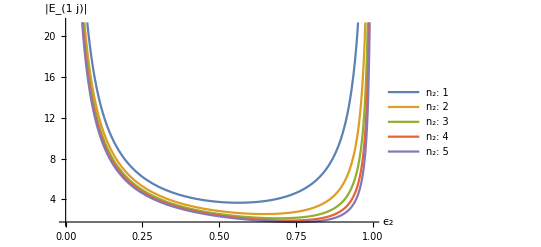

```mathematica
pErrorSecondLevel = Plot[{AbsErrorTabE1j [[1,2]] /.  {e1 -> 1- e2}, AbsErrorTabE1j [[2,2]] /.  {e1 -> 1- e2},AbsErrorTabE1j [[3,2]] /.  {e1 -> 1- e2}, AbsErrorTabE1j [[4,2]] /.  {e1 -> 1- e2}, AbsErrorTabE1j [[5,2]] /.  {e1 -> 1- e2}}, {e2, 0, 1},AxesLabel->{Subscript[ϵ, 2], "|E_(1  j)|"}, PlotLegends->{"n_2: 1","n_2: 2","n_2: 3","n_2: 4","n_2: 5"}]
```

```mathematica
Export["plots/abs_E1j_vs_e2_n2_1-5.png",pErrorSecondLevel,ImageSize->1200]
```

plots/abs_E1j_vs_e2_n2_1-5.png

```mathematica
AbsErrNs11 =<< "abs_error_results/AbsError_n2_1_n3_1.ml";
```

```mathematica
AbsErrNs12 =<< "abs_error_results/AbsError_n2_1_n3_2.ml";
```

```mathematica
AbsErrNs13 =<< "abs_error_results/AbsError_n2_1_n3_3.ml";
```

```mathematica
AbsErrNs21 =<< "abs_error_results/AbsError_n2_2_n3_1.ml";
```

```mathematica
AbsErrNs22 =<< "abs_error_results/AbsError_n2_2_n3_2.ml";
```

```mathematica
AbsErrNs31 =<< "abs_error_results/AbsError_n2_3_n3_1.ml";
```

```mathematica
AbsErrNs31/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5} /. {e3 -> 0.6}
```

-1.73411×10^45

```mathematica
p13 = Plot3D[AbsErrNs13 /.{e1-> (1-e3)*e1share ,e2-> (1-e3)*(1 - e1share) }, {e3, 0, 1} ,{e1share, 0, 1},  AxesLabel->{Subscript[ϵ, 3],Subscript[ϵ, 1]/(Subscript[ϵ, 1]+Subscript[ϵ, 2]), "|E_(1  jk)|"}, PlotLabel->"n_2=1, n_3=3", PlotPoints->50]
```

-Graphics3D-

```mathematica
p22 = Plot3D[AbsErrNs22 /.{e1-> (1-e3)*e1share ,e2-> (1-e3)*(1 - e1share) }, {e3, 0, 1} ,{e1share, 0, 1},  AxesLabel->{Subscript[ϵ, 3],Subscript[ϵ, 1]/(Subscript[ϵ, 1]+Subscript[ϵ, 2]), "|E_(1  jk)|"},PlotLabel->"n_2=2, n_3=2", PlotPoints->100]
```

-Graphics3D-

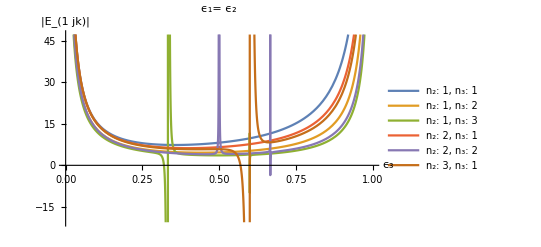

```mathematica
pErrorThirdLevel = Plot[{AbsErrNs11/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5},AbsErrNs12/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5},
AbsErrNs13/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5},
AbsErrNs21/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5},
AbsErrNs22/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5},
AbsErrNs31/.  {e2 -> (1- e3)*0.5, e1-> (1- e3)*0.5}
}, 
{e3, 0, 1},AxesLabel->{Subscript[ϵ, 3], "|E_(1  jk)|"}, PlotLabel->"ϵ_1= ϵ_2",PlotLegends-> {"n_2: 1, n_3: 1","n_2: 1, n_3: 2", "n_2: 1, n_3: 3","n_2: 2, n_3: 1","n_2: 2, n_3: 2","n_2: 3, n_3: 1"}, PlotPoints->100]
```

```mathematica
Export["plots/abs_E1jk_vs_e3.png",pErrorThirdLevel, ImageSize -> 1200]
```

plots/abs_E1jk_vs_e3.png

```mathematica
Export["plots/abs_E1jk_vs_e3_vs_e1share_ns_13.png",p13]
```

plots/abs_E1jk_vs_e3_vs_e1share_ns_13.png

```mathematica
Export["plots/abs_E1jk_vs_e3_vs_e1share_ns_22.png",p22]
```

plots/abs_E1jk_vs_e3_vs_e1share_ns_22.png

### Variance at level l

Variance at level l, with fixed branching constant, and equal split between lower level epsilons.
Something is off in these equations.  It doesn’t match the level 2 and 3 variance plots even with the same parameters.  See plots of VarEh(2, ...) and Var1j below

```mathematica
VarEh [l_, ns_, es_] := 1/ns[[l]]^2 * (2/es[[1]]^2 * 1/(Times@@Drop[ns,-1]) + Sum[Product[1/ns[[k]]^2, {k, j+1, l-1}], {j, 2, l-1}] ) + (1  - 1/ns[[l]])*2/es[[l]]^2
(*Sum[(1- 1/ns[[l-j]])*(2/es[[l-j]]^2)*Product[1/ns[[l-k]]^2, {k, 0 , j-1}], {j, 0, l-1}]*)
```

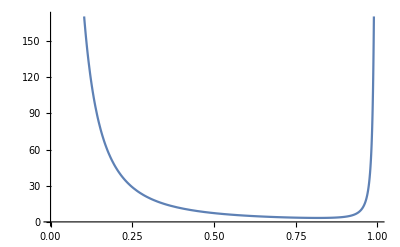

```mathematica
Plot[VarEh[2, {1,10}, {1-e2, e2}], {e2, 0, 1}]
```

```mathematica
VarEh[3, {1,10,10},{1-e2-e3, e2, e3}]
```

1/100 (1+1/(5 (1-e2-e3)^2))+9/(5 e3^2)

```mathematica
Reduce[ 0 < e2 < 1 && 0 < e3 < 1 && 0 < 1 - e2  - e3  < 1, {e2, e3}]
```

0<e2<1&&0<e3<1-e2

```mathematica
Manipulate[Plot3D[VarEh[3, {1,n2,n3},{(1-e2-e3)*4, e2*4, e3*4}], {e2, 0, 1}, {e3, 0, 1}, AxesLabel->{"e2", "e3", "Var(E_(1  jk))"},Mesh->False,
RegionFunction->Function[{e2, e3}, 0 < e2 < 1 && 0 < e3 < 1 && 0 < 1 - e2  - e3  < 1]], {{n2, 10, Subscript[n, 2]}, 1,20,1,Appearance->"Labeled"},{{n3, 10, Subscript[n, 3]}, 1,20,1,Appearance->"Labeled"}]
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
Plot3D[VarEh[2, {1,n2}, {(1-e2)*4, e2*4}], {e2, 0, 1}, {n2, 1,30 }, AxesLabel->{"e_2", "n_2", "Var(E_(1  j))"}, PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[VarEh[3, {1,10,10}, {(1-e3)*e1share*4 ,(1-e3)*4*(1 - e1share) , e3}*4], {e3, 0, 1} ,{e1share, 0, 1},  AxesLabel->{Subscript[ϵ, 3],Subscript[ϵ, 1]/(Subscript[ϵ, 1]+Subscript[ϵ, 2]), "Var(E_(1  jk))"}, PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[VarEh[3, {1,3,10},{(1-e2-e3)*4, e2*4, e3*4}], {e2, 0, 1}, {e3, 0, 1}, AxesLabel->{"e_2", "e_3", "Var(E_(1  jk))"},
RegionFunction->Function[{ e2, e3}, 0 < e2 < 1 && 0 < e3 < 1 && 0 < 1 - e2  - e3  < 1], PlotPoints->50]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
Manipulate[Plot[VarEh[l, n, el*eps, (1-el)*eps/(l-1)], {el, 0,1}, AxesLabel->{Subscript[ϵ, l], "Var(E_h)"}], {{l, 3, l}, 2,10,1,Appearance->"Labeled"},{{n, 10, n}, 1,20,1,Appearance->"Labeled"},{{nl, 10, nl}, 1,20,1,Appearance->"Labeled"}, {{eps,4, ϵ}, 1,8,Appearance->"Labeled"}]
```

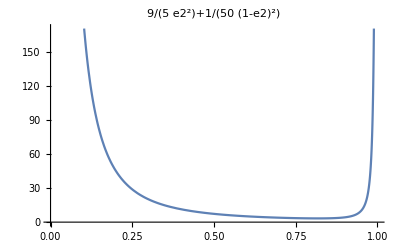

```mathematica
Plot[VarEh[2, {1,10}, {1-e2, e2}], {e2, 0, 1}, PlotLabel->VarEh[2, {1,10}, {1-e2, e2}]]
```

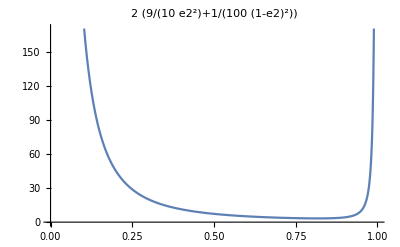

```mathematica
Plot[Var1j[10, 1-el, el], {el, 0, 1},PlotLabel->Var1j[10, 1-e2, e2]]
```

```mathematica
VarEh[2, {1,10}, {1-e2, e2}]
```

1/(50 (1-e2)^2)+9/(5 e2^2)

```mathematica
Var1j[10, 1-e2, e2]
```

2 (1/(100 (1-e2)^2)+9/(10 e2^2))

```mathematica
VarEh[2, {1,10}, {1-e2, e2}]
```

1/(50 (1-e2)^2)+9/(5 e2^2)

```mathematica
VarEh[1, {1,10}, {e2, e2}]
```

2/e2^2

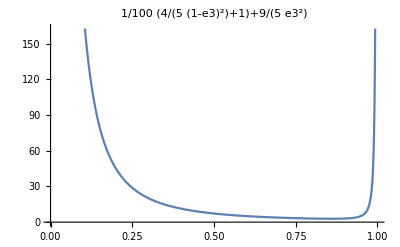

```mathematica
Plot[VarEh[3, {1,10,10}, {(1-e3)/2,(1-e3)/2, e3}], {e3, 0, 1}, PlotLabel->VarEh[3, {1,10,10}, {(1-e3)/2,(1-e3)/2, e3}]]
```

```mathematica
Var1jk[10,10, (1-e3)/2,(1-e3)/2, e3]
```

91/(1250 (1-e3)^2)+11/(5 e3^2)

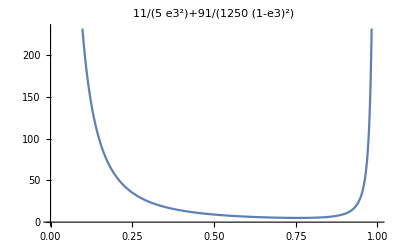

```mathematica
Plot[Var1jk[10,10, (1-e3)/2,(1-e3)/2, e3], {e3, 0, 1}, PlotLabel->Var1jk[10,10, (1-e3)/2,(1-e3)/2, e3]]
```